Cadenas de caracteres y plantillas

Los patrones para cadenas de caracteres funcionan de manera muy parecida a los otros patrones en Wolfram Language, salvo que operan con secuencias de caracteres en cadenas en vez de partes de expresiones. En un patrón para cadena, pueden combinarse conceptos de patrones, tales como _, con cadenas de caracteres como "abc" usando ~~.

Con esto se eligen todos los casos de + seguidos de un solo carácter:

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~_]
```

{+s,+p,+q,+e}

Ahora se eligen tres caracteres después de cada +:

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~_~~_~~_]
```

{+str,+pat,+qui,+eas}

Use el nombre x para el carácter después de cada +, y regrese ese carácter enmarcado:

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~x_->Framed[x]]
```

{s,p,q,e}

En un patrón para cadena de caracteres, _ representa cualquier carácter solo. _ _ (“doble guión-bajo”) representa cualquier secuencia de uno o más caracteres, y _ _ _ (“triple guión-bajo”) representa cualquier secuencia de cero o más caracteres. _ _ y _ _ _ generalmente atraparán tanto como puedan de la cadena.

Elija la secuencia de caracteres entre [ y ]:

```mathematica
StringCases["the [important] word", "["~~x__~~"]"->Framed[x]]
```

{important}

_ _ normalmente hace la coincidencia con la secuencia de caracteres más larga que se pueda:

```mathematica
StringCases["now [several] important [words]", "["~~x__~~"]"->Framed[x]]
```

{several] important [words}

Shortest fuerza la coincidencia más corta:

```mathematica
StringCases["now [several] important [words]", "["~~Shortest[x__]~~"]"->Framed[x]]
```

{several,words}

StringCases elige los casos de un patrón dado en una cadena de caracteres. StringReplace efectúa sustituciones.

Efectúe sustituciones en caracteres de la cadena:

```mathematica
StringReplace["now [several] important [words]", {"["->"<<","]"->">>"}]
```

now <<several>> important <<words>>

Efectúe sustituciones para patrones, usando :> para calcular ToUpperCase en cada caso:

```mathematica
StringReplace["now [several] important [words]", "["~~Shortest[x__]~~"]":>ToUpperCase[x]]
```

now SEVERAL important WORDS

Use NestList para aplicar repetidamente una sustitución en una cadena:

```mathematica
NestList[StringReplace[#,{"A"->"AB","B"->"BA"}]&,"A",5]
```

{A,AB,ABBA,ABBABAAB,ABBABAABBAABABBA,ABBABAABBAABABBABAABABBAABBABAAB}

StringMatchQ prueba si una cadena coincide con un patrón.

Seleccione aquellas palabras comunes del inglés que coincidan con el patrón “comienza con a y termina con b":

```mathematica
Select[WordList[ ],StringMatchQ[#,"a"~~___~~"b"]&]
```

{absorb,adsorb,adverb,alb,aplomb}

Puede usarse | y .. en patrones para cadenas, de la misma forma que en patrones ordinarios.

Elija cualquier secuencia de A o B repetidas:

```mathematica
StringCases["the AAA and the BBB and the ABABBBABABABA",("A"|"B")..]
```

{AAA,BBB,ABABBBABABABA}

En un patrón para cadena, LetterCharacter representa cualquier carácter que sea una letra, DigitCharacter cualquier carácter que sea un dígito, y Whitespace cualquier secuencia de espacios “en blanco”, tales como los espaciadores.

Elija las secuencias de caracteres dígitos:

```mathematica
StringCases["12 and 123 and 4567 and 0x456",DigitCharacter..]
```

{12,123,4567,0,456}

Elija las secuencias de caracteres dígitos que tengan a cada lado un espacio en blanco:

```mathematica
StringCases["12 and 123 and 4567 and 0x456",Whitespace~~DigitCharacter..~~Whitespace]
```

{ 123 , 4567 }

En situaciones prácticas es común querer cambiar de cadenas de caracteres a listas, o viceversa. Puede separarse una cadena en una lista de porciones utilizando StringSplit.

Separe una cadena en una lista de porciones, usando por defecto los espacios para hacer la separación:

```mathematica
StringSplit["a string to split"]
```

{a,string,to,split}

Ahora se usa un patrón de cadena para decidir dónde hacer la separación:

```mathematica
StringSplit["you+can+split--at+any--delimiter","+"|"--"]
```

{you,can,split,at,any,delimiter}

Dentro de una cadena de caracteres, hay un carácter especial para un cambio de línea, que indica en qué parte debe cambiar de línea la cadena. Dicho carácter se representa con \n.

Separe en cada cambio de línea:

```mathematica
StringSplit["first line
second line
third line","\n"]
```

{first line,second line,third line}

StringJoin junta cualquier lista de cadenas de caracteres. Sin embargo, en la práctica hay veces en que se quiere insertar algo entre las cadenas antes de juntarlas. Esto se hace con StringRiffle.

Junte cadenas, intercalando la cadena "---" entre ellas:

```mathematica
StringRiffle[{"a","list","of","strings"},"---"]
```

a---list---of---strings

Cuando se arma una cadena, frecuentemente se quiere convertir alguna expresión arbitraria de Wolfram Language en una cadena de caracteres. Esto se puede hacer usando TextString.

TextString convierte números y otras expresiones de Wolfram Language en cadenas de caracteres:

```mathematica
StringJoin["two to the ",TextString[50]," is ",TextString[2^50]]
```

two to the 50 is 1125899906842624

Una manera más conveniente de crear cadenas de caracteres a partir de expresiones es el uso de plantillas para cadenas. Las plantillas para cadenas trabajan como funciones puras dado que tienen ranuras en las que pueden insertarse argumentos.

En una plantilla para cadena, cada `` es una ranura para un argumento sucesivo:

```mathematica
StringTemplate["first `` then ``"][100,200]
```

first 100 then 200

Las ranuras con nombre eligen elementos de una asociación:

```mathematica
StringTemplate["first: `a`; second `b`; first again `a`"][<|"a"->"AAAA", "b"->"BB BBB"|>]
```

first: AAAA; second BB BBB; first again AAAA

Se puede insertar cualquier expresión en una plantilla para cadena encerrándola entre <*...*>. El valor de la expresión se calcula al momento de aplicar la plantilla.

Evalúe la <*...*> cuando se aplica la plantilla; no se requieren argumentos:

```mathematica
StringTemplate["2 to the 50 is <* 2^50 *>"][ ]
```

2 to the 50 is 1125899906842624

Use ranuras en la plantilla (` es el carácter acento invertido):

```mathematica
StringTemplate["`1` to the `2` is <* #1^#2 *>"][2,50]
```

2 to the 50 is 1125899906842624

La expresión en la plantilla se evalúa al aplicar la plantilla:

```mathematica
StringTemplate["the time now is <* Now *>"][ ]
```

the time now is Wed 16 Sep 2015 16:50:43

Vocabulario

patt_1~~patt_2 |   | secuencia de patrones de cadena de caracteres 
Shortest[patt] |   | la cadena más corta que coincida 
StringCases[string,patt] |   | los casos en una cadena de caracteres que coincidan con
un patrón
StringReplace[string,patt→val] |   | sustituye un patrón dentro de una cadena de caracteres
StringMatchQ[string,patt] |   | comprueba si una cadena de caracteres coincide 
con un patrón 
LetterCharacter |   | forma de patrón que coincide con una letra 
DigitCharacter |   | forma de patrón que coincide con un dígito 
Whitespace |   | forma de patrón que coincide con espacios, etc.
\n |   | carácter que indica cambio de línea 
StringSplit[string] |   | separa una cadena de caracteres en una lista de
porciones 
StringJoin[{string_1,string_2, ...}] |   | junta cadenas de caracteres 
StringRiffle[{string_1,string_2, ...},m] |   | junta cadenas de caracteres, insertando m entre ellas 
TextString[expr] |   | forma una cadena de texto a partir de algo 
StringTemplate[string] |   | crea una plantilla de cadena de caracteres para aplicar 
`` |   | ranura en una plantilla de cadena de caracteres
<*...*> |   | expresión para ser evaluada dentro de una plantilla
de cadena de caracteres

"8 Exercises Available" | "Get Started »"

Sustituya cada espacio en "1 2 3 4" con "---". »

| Expected output: |  
  | "1---2---3---4" |

Obtenga una lista ordenada de todas las secuencias de 4 dígitos (que posiblemente representan fechas) en el artículo de Wikipedia sobre “computers”. »

| Sample expected output: |  
  | {"1000","1235","1357","1357","1500","1595","1613","1620","1630","1770","1833","1872","1872","1876","1876","1888","1901","1906","1920","1927","1930","1931","1934","1936","1936","1938","1939","1941","1942","1943","1943","1943","1944","1945","1945","1945","1945","1947","1947","1947","1948","1950","1950","1951","1951","1952","1953","1953","1955","1955","1955","1957","1958","1958","1959","1970","1970","1990","2000","2000","2013","2400","2400","2468","4004","5000"} |

Extraiga los “encabezados” en el artículo de Wikipedia sobre “computers”, que se indican mediante cadenas de caracteres que comienzan y terminan con "===". »

| Sample expected output: |  
  | {" Pre-twentieth century "," First general-purpose computing device "," Later Analog computers "," Digital computer development ","= Electromechanical ","= Vacuum tubes and digital electronic circuits ","= Stored programs ","= Transistors ","= Integrated circuits "," Mobile computers become dominant "," Stored program architecture "," Machine code "," Programming language ","= Low-level languages ","= High-level languages/Third Generation Language "," Fourth Generation Languages "," Program design "," Bugs "," Control unit "," Central Processing unit (CPU) "," Arithmetic logic unit (ALU) "," Memory "," Input/output (I/O) "," Multitasking "," Multiprocessing "," Computer architecture paradigms "," Unconventional computing "," Artificial intelligence "," History of computing hardware "," Other hardware topics "," Firmware "," Liveware "," Based on uses "," Based on sizes "} |

Use una plantilla para cadena de caracteres para hacer una rejilla con los resultados de la forma i+j=... para i y j hasta el 9. »

| Expected output: |  
  | "1+1=2" | "1+2=3" | "1+3=4" | "1+4=5" | "1+5=6" | "1+6=7" | "1+7=8" | "1+8=9" | "1+9=10"
"2+1=3" | "2+2=4" | "2+3=5" | "2+4=6" | "2+5=7" | "2+6=8" | "2+7=9" | "2+8=10" | "2+9=11"
"3+1=4" | "3+2=5" | "3+3=6" | "3+4=7" | "3+5=8" | "3+6=9" | "3+7=10" | "3+8=11" | "3+9=12"
"4+1=5" | "4+2=6" | "4+3=7" | "4+4=8" | "4+5=9" | "4+6=10" | "4+7=11" | "4+8=12" | "4+9=13"
"5+1=6" | "5+2=7" | "5+3=8" | "5+4=9" | "5+5=10" | "5+6=11" | "5+7=12" | "5+8=13" | "5+9=14"
"6+1=7" | "6+2=8" | "6+3=9" | "6+4=10" | "6+5=11" | "6+6=12" | "6+7=13" | "6+8=14" | "6+9=15"
"7+1=8" | "7+2=9" | "7+3=10" | "7+4=11" | "7+5=12" | "7+6=13" | "7+7=14" | "7+8=15" | "7+9=16"
"8+1=9" | "8+2=10" | "8+3=11" | "8+4=12" | "8+5=13" | "8+6=14" | "8+7=15" | "8+8=16" | "8+9=17"
"9+1=10" | "9+2=11" | "9+3=12" | "9+4=13" | "9+5=14" | "9+6=15" | "9+7=16" | "9+8=17" | "9+9=18" |

Encuentre los nombres en inglés de aquellos enteros menores que 50 que contengan una “i” en algún lugar antes de una “e”. »

| Expected output: |  
  | {"five","nine","thirteen","fifteen","sixteen","eighteen","nineteen","twenty-five","twenty-nine","thirty-one","thirty-three","thirty-five","thirty-seven","thirty-eight","thirty-nine","forty-five","forty-nine"} |

Convierta a mayúsculas las palabras que consten de 2 letras en la primera oración del artículo de Wikipedia sobre “computers”. »

| Sample expected output: |  
  | "A computer IS a general-purpose device that can BE programmed TO carry out a set OF arithmetic OR logical operations automatically." |

Haga una gráfica de barras, con etiquetas, del número de países cuyos nombres, formados con TextString, comiencen con cada letra posible. »

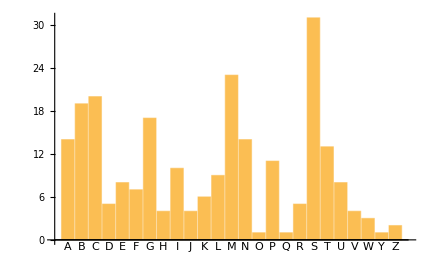
| Expected output: |  
  | -Graphics- |

Encuentre un código más simple para 
Grid[Table[StringJoin[TextString[i],"^",TextString[j],"=",TextString[i^j]],{i,5},{j,5}]]. »

| Expected output: |  
  | "1^1=1" | "1^2=1" | "1^3=1" | "1^4=1" | "1^5=1"
"2^1=2" | "2^2=4" | "2^3=8" | "2^4=16" | "2^5=32"
"3^1=3" | "3^2=9" | "3^3=27" | "3^4=81" | "3^5=243"
"4^1=4" | "4^2=16" | "4^3=64" | "4^4=256" | "4^5=1024"
"5^1=5" | "5^2=25" | "5^3=125" | "5^4=625" | "5^5=3125" |

Preguntas y respuestas

¿Cómo se dice en voz alta ~~?

Por lo general se dice “tilde tilde”. La función subyacente es StringExpression.

¿Cómo se digita `` para insertar una ranura en una plantilla de cadena de caracteres?

Es un par de acentos invertidos que, en muchos teclados, aparecen en el extremo superior izquierdo, junto con la ~ (tilde).

¿Se pueden escribir reglas para la comprensión de lenguaje natural?

Sí, pero el tema no se cubre en el libro. La función clave es GrammarRules.

¿Qué hace TextString cuando se encuentra con algo que no tiene una forma textual obvia?

Trata de lograr algo humanamente legible pero, si no puede, lo devuelve en términos de InputForm.

Notas técnicas

Existe una correspondencia entre patrones para cadenas de caracteres y patrones para secuencias en listas. SequenceCases es el análogo para listas de StringCases para cadenas.

La opción Overlaps especifica si se permiten superposiciones en coincidencias de cadenas de caracteres, o si no se permiten. Funciones diferentes tienen diferentes valores por defecto.

Por defecto, los patrones para cadenas de caracteres dan coincidencia con las secuencias más largas; entonces, hay que especificar Shortest si se desea lo contrario. Por defecto, los patrones para expresiones dan coincidencia con las secuencias más cortas.

Entre otras funciones para patrones de cadenas de caracteres, se tienen Whitespace, NumberString, WordBoundary, StartOfLine, EndOfLine, StartOfString y EndOfString.

En cualquier parte de un patrón simbólico para cadena de caracteres, puede usarse RegularExpression para incluir sintaxis de expresiones regulares, tales como x* y [abc][def].

TextString trata de lograr una versión textual de algo, que sea legible por personas, desechando cosas como los detalles de gráficas. ToString[InputForm[expr]] da una versión completa, que pueda usarse para entrada subsecuente.

Pueden compararse cadenas de caracteres usando operaciones tales como SequenceAlignment. Esto es especialmente útil en la bioinformática.

FileTemplate, XMLTemplate y NotebookTemplate hacen lo análogo de StringTemplate para archivos, documentos XML (y HTML) y cuadernos.

Wolfram Language incluye la función TextSearch, para hacer búsquedas de texto en colecciones grandes de archivos.

Para explorar más

Guía para patrones en cadenas de caracteres en Wolfram Language »